```mathematica
result = DSolveValue[{3600 y'[t]+1970 y''[t]+87 Derivative[3][y][t]+Derivative[4][y][t]==750*HeavisideTheta[t],y[0]==0,y'[0]==0,y''[0]==0,y'''[0]==0},y[t],t]
```

(ⅇ^(-45 t) (2432-3483 ⅇ^(5 t)+162000 ⅇ^(43 t)-160949 ⅇ^(45 t)+294120 ⅇ^(45 t) t) HeavisideTheta[t])/1411776

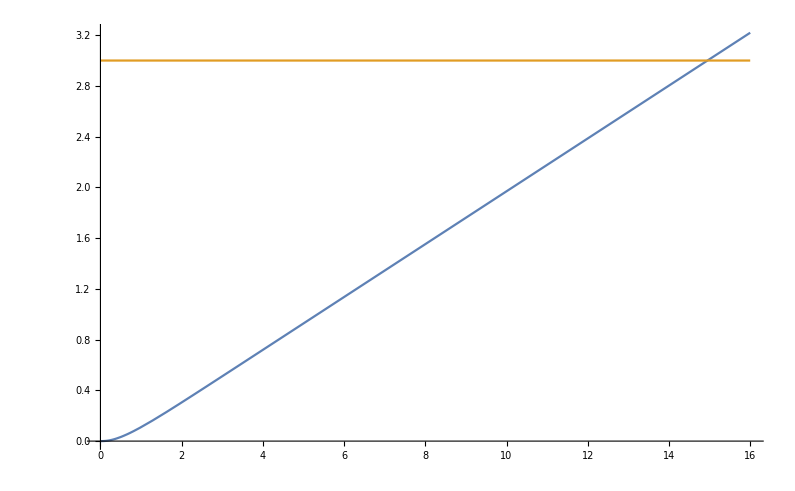

```mathematica
Plot[{result,3HeavisideTheta[t]},{t,0,16}]
```